# Tour de TNB Appendix: 1.1 Sharpest Curves 1.2 Feed Zones

## Problem Statement

```mathematica
2.1
```

```mathematica
Clear[r]
```

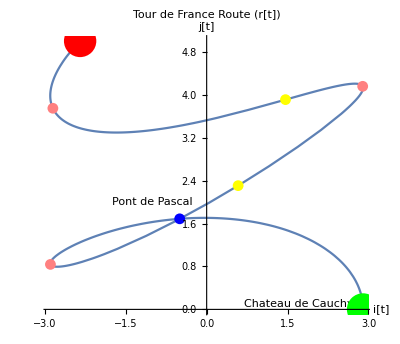

```mathematica
x[t]=2.9Cos[3.2π*t];
y[t]=Sin[4π*t]+5t;
r[t_]={2.9Cos[3.2π*t],(Sin[4π*t]+5t)};(*where t is in hours*)
Plot1=ParametricPlot[r[t],{t,0,1},AxesLabel->{Style["i[t]",Medium],Style["j[t]",Medium]},PlotLabel->Style["Tour de France Route (r[t])",FontSize->14]];(*Plot villages, bridge*)
deCauchy = Graphics[{Green,Disk[{2.9,0},.3]}];
text1=Graphics[Text[Style["Chateau de Cauchy",Medium],{1.7,.1}]];
deLaplace = Graphics[{Red,Disk[{2.9Cos[3.2π],(Sin[4π]+5)},.3]}];
text2=Graphics[Text[Style["Chateau de Laplace",Medium],{2.9Cos[3.2π]+1.2,(Sin[4π]+5.12)}]];
PontdePascal = Graphics[{Blue,Disk[{-0.5001021138107051,1.6874740367935988},.1]}];
text3=Graphics[Text[Style["Pont de Pascal",Medium],{-1,2}]];
Show[{Plot1,deCauchy,deLaplace,PontdePascal,text1,text2,text3,hb1,hb2,fz2,fz3,hb3}]
```

```mathematica
(*Intersects for the Pont de Pascal at time t=0.17349 found by solving for when the function equals itselt. Also NOTE; FEED ZONES => Yellow dots; HALE BALES => Pink dots*)
```

```mathematica
2.2
```

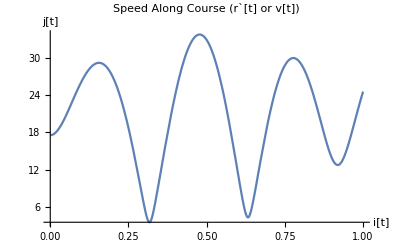

```mathematica
Velocity=D[r[t],t];(*velocity vector in km/hour*)
MagSpeed=Norm[Velocity];(*length of velocity vector or MAGNITUDE*)
Plot[MagSpeed,{t,0,1},AxesLabel->{Style["i[t]",Small],Style["j[t]",Small]},PlotLabel->Style["Speed Along Course (r`[t] or v[t])",FontSize->14]]
avgspeed = NIntegrate[MagSpeed,{t,0,1}]/1;(*integral of speed length vector from t=0 -> t=1 in km/hr*)
```

## 2.3

```mathematica
TotalLength=NIntegrate[MagSpeed,{t,0,1}](*sum of tangent lengths in km*)
Norm[r[1]-r[0]](*direct route length in km*)
```

21.0979

7.24721

## 2.4

```mathematica
d[s_?NumericQ]:=NIntegrate[MagSpeed,{t,0,s}];
FindRoot[d[t]==1,{t,1}](*time that will be 1 km away from 1st village de Cauchy*)
d[s_?NumericQ]:=NIntegrate[MagSpeed,{t,0,s}];
FindRoot[d[t]==d[1]-1,{t,1}](*time that will be i km away from 2nd village de Laplace*)
```

{t→0.0531995}

{t→0.950194}

## 2.5(a-b)

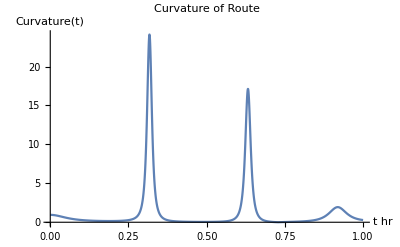

```mathematica
Acc=r''[t];(*Accleration vector km/hr^2*)
TOP=Cross[{-29.15397982531328 Sin[10.053096491487338 t],5+4 π Cos[4 π t],0},{-293.0877722947496 Cos[10.053096491487338 t],-16 π^2 Sin[4 π t],0}];(*r`[t]x r``[t]*)
KK=Norm[TOP]/MagSpeed^3;(*curvature formula*)
Plot[KK,{t,0,1},PlotRange->All];
Show[%337,AxesLabel->{HoldForm[t hr],HoldForm[Curvature[t]]},PlotLabel->HoldForm[Curvature of Route],LabelStyle->{GrayLevel[0]}]
```

## 2.6(a-c)

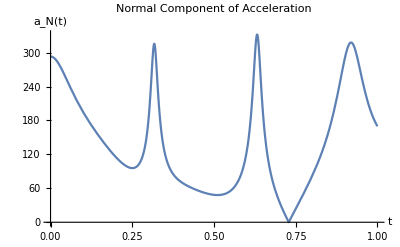

```mathematica
Subscript[a, N]=(MagSpeed^2)*KK;
Plot[Subscript[a, N],{t,0,1}];
Show[%362,AxesLabel->{HoldForm[t],HoldForm[Subscript[a, N][t]]},PlotLabel->HoldForm[Normal Component of Acceleration],LabelStyle->{GrayLevel[0]}]
```

## 2.7

```mathematica
FindMaximum[Subscript[a, N],{t,.65}](*point where there should be a hay bales*)
FindMaximum[Subscript[a, N],{t,.3}]
FindMaximum[Subscript[a, N],{t,.92}]
```

{331.98,{t→0.631983}}

{315.667,{t→0.31728}}

{317.845,{t→0.919249}}

## 2.8

```mathematica
FindMinimum[KK,{t,.2}](*feed zones*)(*NOTE each zone is .3 hr or 18 minutes apart*)
```

{0.15709,{t→0.188415}}

```mathematica
FindMinimum[KK,{t,.5}]
```

{0.0441791,{t→0.488905}}

```mathematica
FindMinimum[KK,{t,.8}]
```

{1.08529×10^-8,{t→0.728697}}

```mathematica
r[.631983](*hay bale*)
```

{2.89286,4.15607}

```mathematica
r[.31728](*hay bale*)
```

{-2.89665,0.83812}

```mathematica
r[.919249](*hay bale*)
```

```mathematica
{-2.8513231651329645,3.7468979667014137}
```

```mathematica
r[.188415](*feed zone*)
```

{-0.921481,1.641}

```mathematica
r[.488905](*feed zone*)
```

{0.583586,2.30555}

```mathematica
r[.728697](*feed zone*)
```

{1.46184,3.908}

```mathematica
hb1 = Graphics[{Pink,Disk[{2.892857118827055,4.1560673539145405},.1]}];
hb2=Graphics[{Pink,Disk[{-2.896652350936423,0.8381200583944702},.1]}];
hb3=Graphics[{Pink,Disk[{-2.8513231651329645,3.7468979667014137},.1]}];
fz1=Graphics[{Yellow,Disk[{-0.921481293295159,1.6410047420409317},.1]}];
fz2=Graphics[{Yellow,Disk[{0.5835860731142549,2.305552389774882},.1]}];
fz3=Graphics[{Yellow,Disk[{1.4618419780796008,3.9080004036515006},.1]}];
```